```mathematica
Get[NotebookDirectory[]<>#]&/@
{
"combine_packages.wls"
};
```

```mathematica
figureNumberSteadyState2DShort="Fig_3";
figureNumberSteadyState2DLong=figureNumberSteadyState2DShort<>"_steady_states";
```

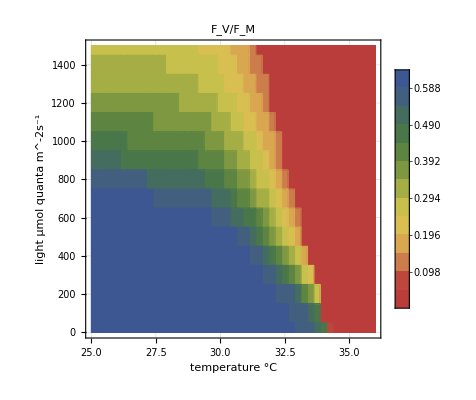

```mathematica
colorSchemes=Join[#->ColorData[{"DarkRainbow","Reverse"}]&/@{FvFm,ϕPSII},{_->ColorData["DarkRainbow"]}];
maxRanges={
c->{0,.75},
_->Full
};
style2Dplot[quant_]:=
{LabelStyle->{14},
FrameLabel->{{"light "<>(L/.units),None},{"temperature "<>(w/.units),None}},
InterpolationOrder->0,
GridLines->Transparent,
PlotLegends->BarLegend[Automatic,LegendMarkerSize->300],
PlotRange->(quant/.maxRanges),
ImageSize->400,
ImagePadding->{{60,10},{45,10}},
Contours->12,
ColorFunction->(quant/.colorSchemes)};
makeFinalPlot[pars_,quant_,options_]:=
ListContourPlot[
Flatten[
Table[
Module[
{parsNew=Join[{w->ww,L->LL},pars]},
{ww,LL,quant/.finalState[parsNew]/.parsNew}
],
{ww,25,36,.25},
{LL,0,1500,100(*25*)}
],
1],
Evaluate@options,
Evaluate@style2Dplot[quant]
];
(Export[NotebookDirectory[]<>figureNumberSteadyState2DLong<>"/"<>figureNumberSteadyState2DShort<>"_light+temperature_bottom"<>".pdf",#];#/. {_EdgeForm,c_?ColorQ,rest__}:>{EdgeForm[Directive[Thin,c]],c,rest})&@(makeFinalPlot[Join[{tmax-> 24 3600},pars[4]],#,{PlotLabel->(#/.names)}])&@FvFm
```

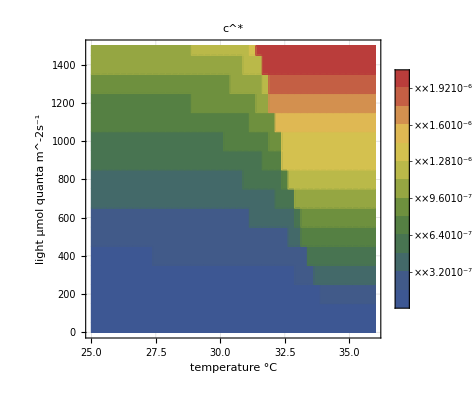
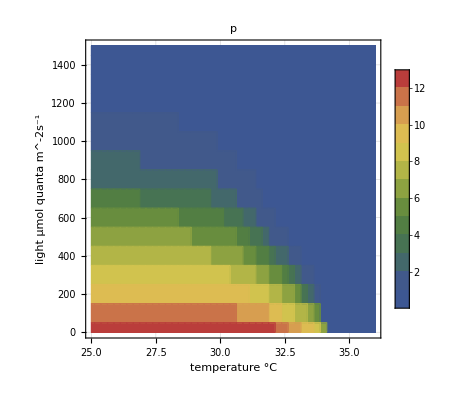
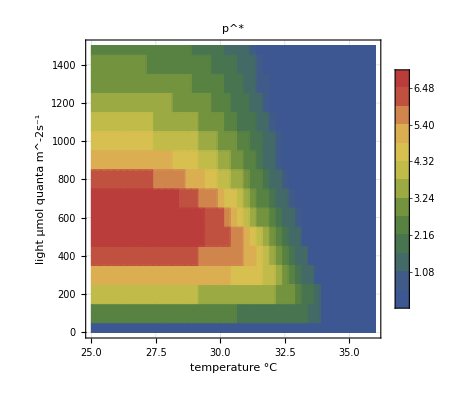
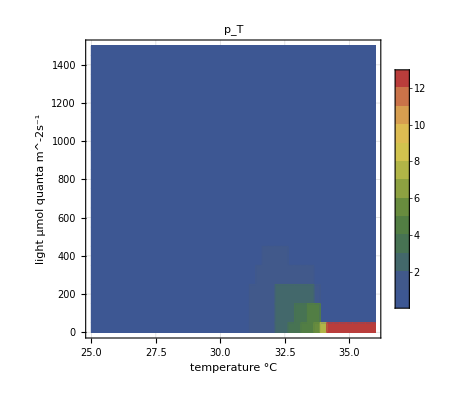
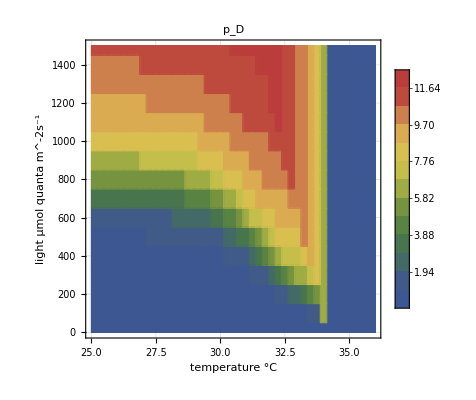
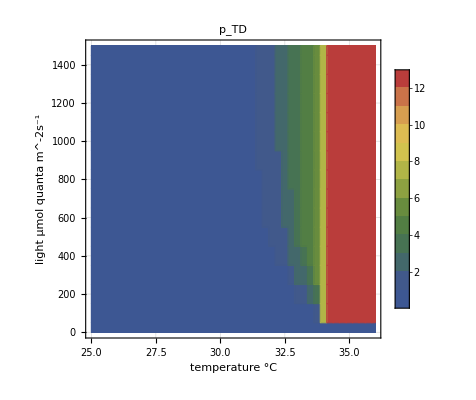
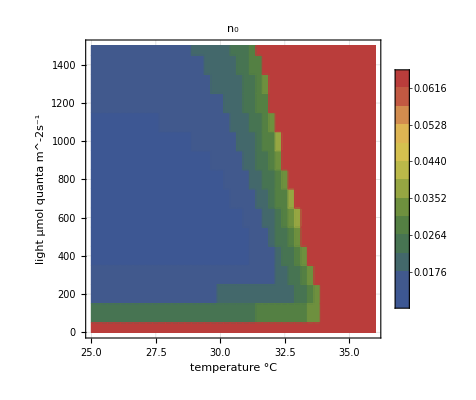
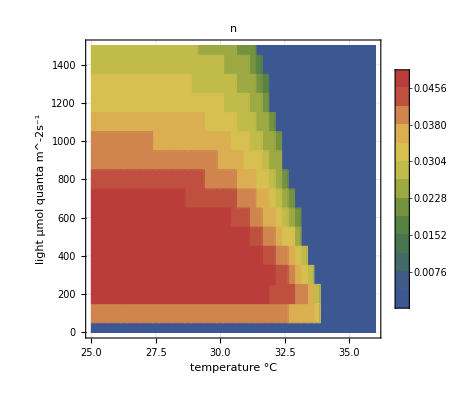
-Graphics-
-Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics-

```mathematica
(Export[NotebookDirectory[]<>figureNumberSteadyState2DLong<>"/"<>figureNumberSteadyState2DShort<>"_light+temperature_SI"<>".pdf",#];#/. {_EdgeForm,c_?ColorQ,rest__}:>{EdgeForm[Directive[Thin,c]],c,rest})&@GridMap[makeFinalPlot[Join[{tmax->24 3600},pars[4]],#,{PlotLabel->#/.names}]&,quants/.c->Nothing,Spacer[30],{Spacings->0}]
```